```mathematica
$Version
```

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

```mathematica
AstroDistance[Here,Entity["Star","Sun"]]
```

0.987678 au

```mathematica
AstroDistance[Here,Entity["PlanetaryMoon","Moon"]]
```

0.00249584 au

```mathematica
UnitConvert[AstroDistance[Here,Entity["PlanetaryMoon","Moon"]]]
```

3.73375×10^8 m

```mathematica
UnitConvert[AstroDistance[Here,Entity["PlanetaryMoon","Moon"]],"Megameters"]
```

373.377 Mm

```mathematica
EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
Table[UnitConvert[AstroDistance[Here,i],"Megameters"],{i,EntityList["Planet"]}]
```

{212526. Mm,253156. Mm,6.37033 Mm,82389.8 Mm,659590. Mm,1.49446×10^6 Mm,2.8×10^6 Mm,4.41716×10^6 Mm}

```mathematica
Table[UnitConvert[AstroDistance[Here,i],"Gigameters"],{i,EntityList["Planet"]}]
```

{212.524 Gm,253.156 Gm,0.00637033 Gm,82.3893 Gm,659.593 Gm,1494.46 Gm,2800. Gm,4417.16 Gm}

```mathematica
Table[UnitConvert[AstroDistance[Here,i],"Terameters"],{i,EntityList["Planet"]}]
```

{0.212524 Tm,0.253156 Tm,6.37033×10^-6 Tm,0.0823893 Tm,0.659594 Tm,1.49446 Tm,2.8 Tm,4.41716 Tm}

```mathematica
Names["*Astro*"]
```

{AstroAngularSeparation,AstroBackground,AstroCenter,AstroDistance,AstroGraphics,AstroGridLines,AstroGridLinesStyle,AstronomicalData,AstroPosition,AstroProjection,AstroRange,AstroRangePadding,AstroReferenceFrame,AstroStyling,AstroZoomLevel}

```mathematica
Subsets[EntityList["Planet"],{2}]
```

{{Mercury,Venus},{Mercury,Earth},{Mercury,Mars},{Mercury,Jupiter},{Mercury,Saturn},{Mercury,Uranus},{Mercury,Neptune},{Venus,Earth},{Venus,Mars},{Venus,Jupiter},{Venus,Saturn},{Venus,Uranus},{Venus,Neptune},{Earth,Mars},{Earth,Jupiter},{Earth,Saturn},{Earth,Uranus},{Earth,Neptune},{Mars,Jupiter},{Mars,Saturn},{Mars,Uranus},{Mars,Neptune},{Jupiter,Saturn},{Jupiter,Uranus},{Jupiter,Neptune},{Saturn,Uranus},{Saturn,Neptune},{Uranus,Neptune}}

```mathematica
Annotation[UndirectedEdge@@#,EdgeWeight->AstroDistance@@#]&/@Subsets[EntityList["Planet"],{2}]
```

{Mercury<->Venus,Mercury<->Earth,Mercury<->Mars,Mercury<->Jupiter,Mercury<->Saturn,Mercury<->Uranus,Mercury<->Neptune,Venus<->Earth,Venus<->Mars,Venus<->Jupiter,Venus<->Saturn,Venus<->Uranus,Venus<->Neptune,Earth<->Mars,Earth<->Jupiter,Earth<->Saturn,Earth<->Uranus,Earth<->Neptune,Mars<->Jupiter,Mars<->Saturn,Mars<->Uranus,Mars<->Neptune,Jupiter<->Saturn,Jupiter<->Uranus,Jupiter<->Neptune,Saturn<->Uranus,Saturn<->Neptune,Uranus<->Neptune}

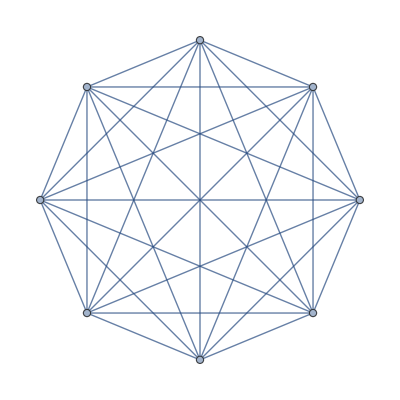

```mathematica
planetDistances=Graph[Annotation[UndirectedEdge@@#,EdgeWeight->AstroDistance@@#]&/@Subsets[EntityList["Planet"],{2}]]
```

```mathematica
tour=FindShortestTour[planetDistances]
```

{77.9637 au,{1,3,4,5,7,8,6,2,1}}

```mathematica
planets=EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
Extract[planets,List/@Last[tour]]
```

{Mercury,Earth,Mars,Jupiter,Uranus,Neptune,Saturn,Venus,Mercury}

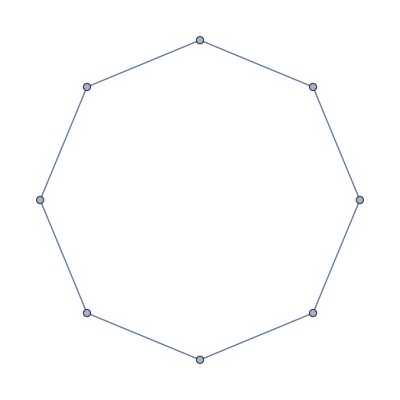

```mathematica
PathGraph[Extract[planets,List/@Last[tour]]]
```

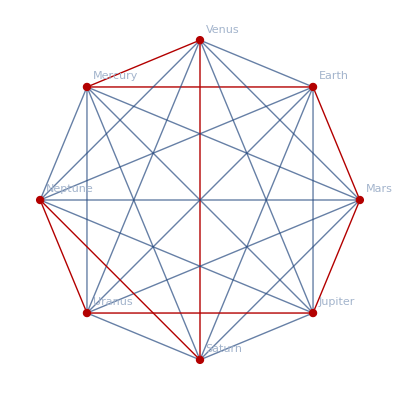

```mathematica
HighlightGraph[planetDistances,PathGraph[Extract[planets,List/@Last[tour]]],VertexLabels->Automatic]
```

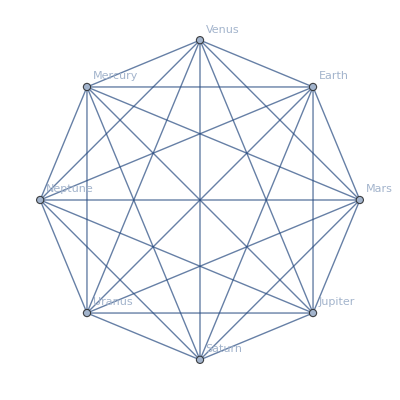

```mathematica
planetSeparations=Graph[Annotation[UndirectedEdge@@#,EdgeWeight->AstroAngularSeparation@@#]&/@Subsets[EntityList["Planet"],{2}],VertexLabels->Automatic]
```

```mathematica
angleTour=FindShortestTour[planetSeparations]
```

{364.96 °,{1,3,4,7,5,8,6,2,1}}

```mathematica
Extract[planets,List/@Last[angleTour]]
```

{Mercury,Earth,Mars,Uranus,Jupiter,Neptune,Saturn,Venus,Mercury}

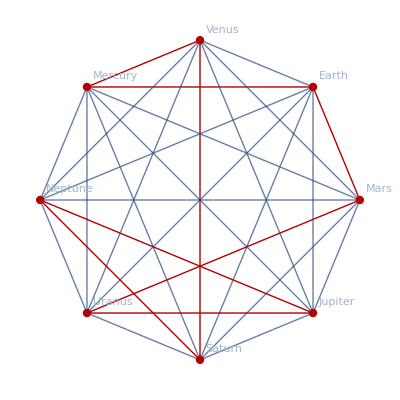

```mathematica
HighlightGraph[planetSeparations,PathGraph[Extract[planets,List/@Last[angleTour]]]]
```

```mathematica
AstroPosition[]
```

AstroPosition::argb: AstroPosition called with 0 arguments; between 1 and 3 arguments are expected.

AstroPosition[]

```mathematica
?AstroPosition
```

```mathematica
AstroPosition[Entity["PlanetaryMoon","Ganymede"],"Equatorial","Cylindrical"]
```

AstroPosition[…]

```mathematica
AstroPosition[Entity["PlanetaryMoon","Ganymede"],"Equatorial","Cartesian"]
```

AstroPosition[…]

```mathematica
AstroPosition[Entity["PlanetaryMoon","Ganymede"],"Galactic","Cartesian"]
```

AstroPosition[…]

```mathematica
AstroPosition[Entity["PlanetaryMoon","Ganymede"],"Horizon","Cartesian"]
```

AstroPosition[…]

```mathematica
AstroPosition[Entity["PlanetaryMoon","Ganymede"],"Horizon","Cartesian"]
```

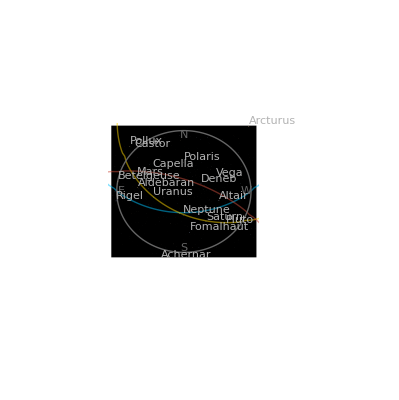

```mathematica
AstroGraphics[]
```

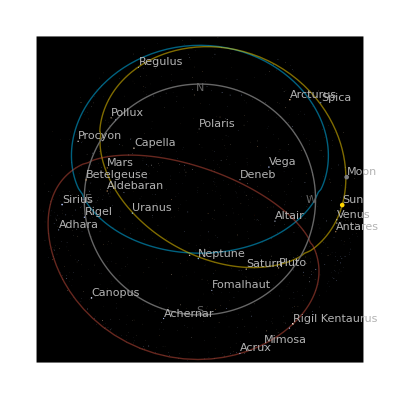

```mathematica
AstroGraphics[AstroCenter->]
```

```mathematica
?AstroGridLines
```

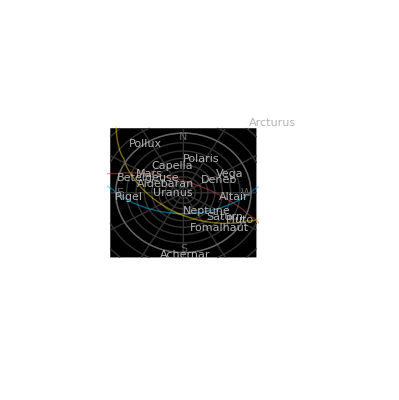

```mathematica
AstroGraphics[AstroGridLines->Automatic]
```

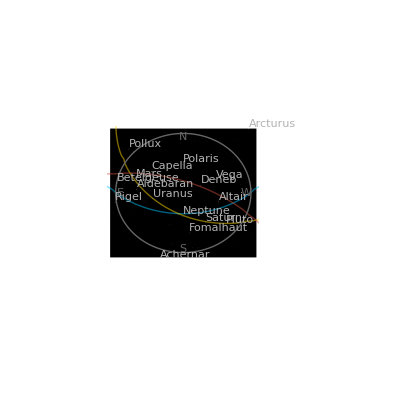

```mathematica
AstroGraphics[AstroGridLines->None]
```

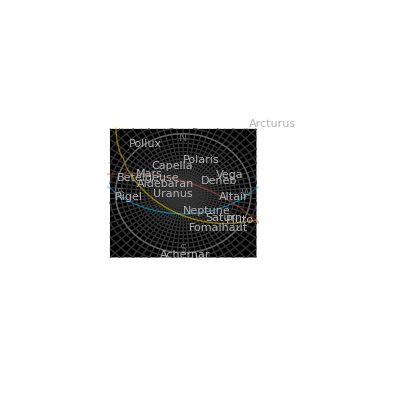

```mathematica
AstroGraphics[AstroGridLines->Quantity[5, "AngularDegrees"]]
```

```mathematica
SystemInformation[]
```

1234567